#### Solution to the eigenfunction problem for a 2D Fokker-Planck Gianni V. Vinci

In the following we are interested to the following Fokker-Planck operator:
L=-∂_x [sΦ(x)-x+(1-1/τ)y] +D/τ(∂_x)^2  +∂_y (y/τ) +D/τ(∂_y)^2 +2 D/τ∂_y ∂_x 
First we find the eigenvalues varying τ:

```mathematica
τs=10^Range[-1,2,0.01];
```

```mathematica
λs=Parallelize[Table[Module[{d=0.8^2/2,τ=τs[[k]],s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},13,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
],{k,1,Length[τs]}]];
```

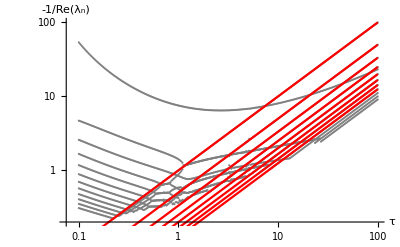

```mathematica
Show[{ListLogLogPlot[Table[Transpose[{τs,-1/Re[λs[[All,n]]]}],{n,13}],PlotRange->{Automatic,{100,0.2}},PlotStyle->Gray,AxesLabel->{"τ","-1/Re(λ_n)"}],Table[LogLogPlot[τ/n,{τ,0.01,100},PlotStyle->Red,PlotRange->All],{n,1,8}]}]
```

Examples of eigenfunctions:

```mathematica
{λ,ϕ}=Module[{d=0.8^2/2,τ=10,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=Quiet[NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},3,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.01}}}]]
];
```

```mathematica
Z=NIntegrate[Evaluate[ϕ[[1]]],{x,-4,4},{y,-4,4}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.952596 and 0.0000420371 for the integral and error estimates.

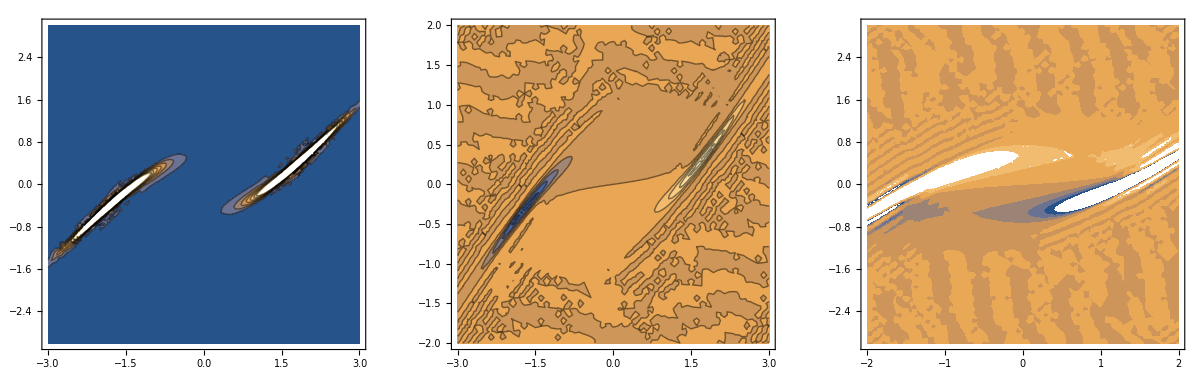

```mathematica
GraphicsRow[{ContourPlot[Abs[Evaluate[ϕ[[1]]]/Z],{x,-3,3},{y,-3,3},PlotRange->{0,0.8}],ContourPlot[Evaluate[ϕ[[2]]],{x,-3,3},{y,-2,2},PlotRange->All],ContourPlot[Evaluate[ϕ[[3]]],{x,-2,2},{y,-3,3},PlotRange->{-0.2,0.2}]}]
```

```mathematica
F[r_,h_,n_,s_]:=Module[{f},f=Evaluate[ϕ[[n]]] /.{x-> s*r +h,y-> h}]
```

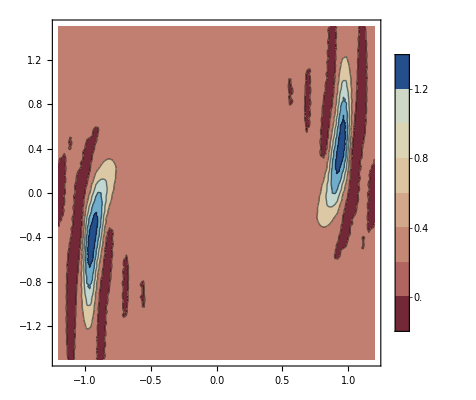

```mathematica
ContourPlot[F[r,h,1,1.5]/Z +0.01,{r,-1.2,1.2},{h,-1.5,1.5},PlotRange->All,PlotLegends->{0.0,0.2,0.4,0.6,0.8,1.0,1.2},ColorFunction->"RedBlueTones"]
```

```mathematica
Plot3D[F[r,h,2,1.5]/Z,{r,-1.2,1.2},{h,-1.5,1.5},PlotRange->All]
```

-Graphics3D-

τ=0.5

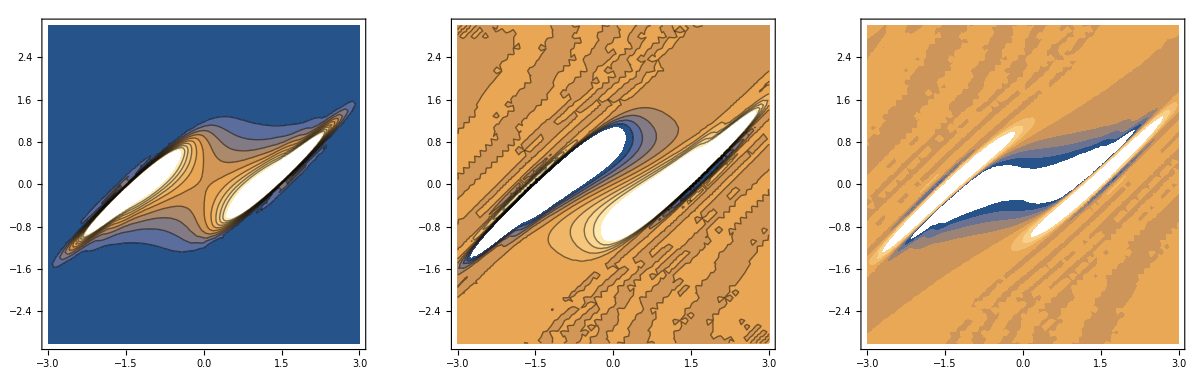

```mathematica
{λ,ϕ}=Module[{d=0.8^2/2,τ=0.5,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=Quiet[NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},3,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.01}}}]]
];
Z=Quiet[NIntegrate[Evaluate[ϕ[[1]]],{x,-4,4},{y,-4,4}]];
GraphicsRow[{ContourPlot[Abs[Evaluate[ϕ[[1]]]/Z],{x,-3,3},{y,-3,3},PlotRange->{0,0.2}],ContourPlot[Evaluate[ϕ[[2]]],{x,-3,3},{y,-3,3},PlotRange->{-0.1,0.1}],ContourPlot[Evaluate[ϕ[[3]]],{x,-3,3},{y,-3,3},PlotRange->{-0.2,0.2}]}]
```

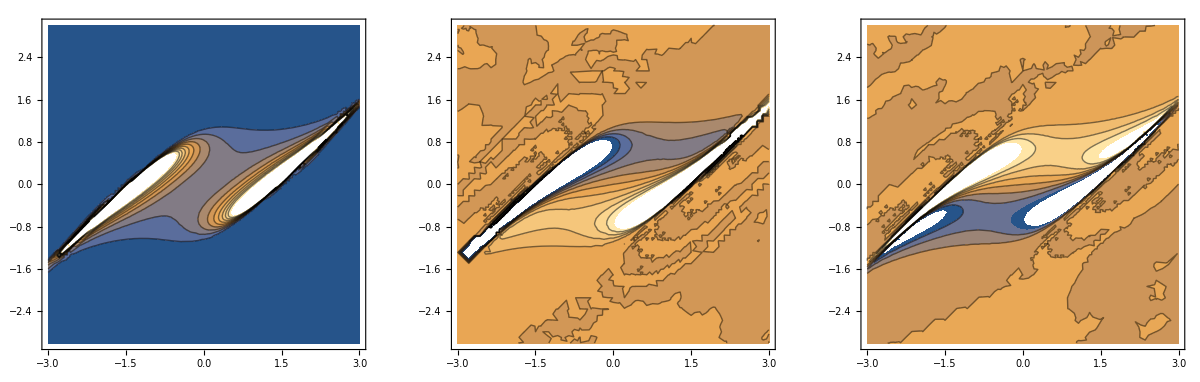

```mathematica
{λ,ϕ}=Module[{d=0.8^2/2,τ=2,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=Quiet[NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},3,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}}]]
];
Z=Quiet[NIntegrate[Evaluate[ϕ[[1]]],{x,-4,4},{y,-4,4}]];
GraphicsRow[{ContourPlot[Abs[Evaluate[ϕ[[1]]]/Z],{x,-3,3},{y,-3,3},PlotRange->{0,0.2}],ContourPlot[Evaluate[ϕ[[2]]],{x,-3,3},{y,-3,3},PlotRange->{-0.1,0.1}],ContourPlot[Evaluate[ϕ[[3]]],{x,-3,3},{y,-3,3},PlotRange->{-0.2,0.2}]}]
```

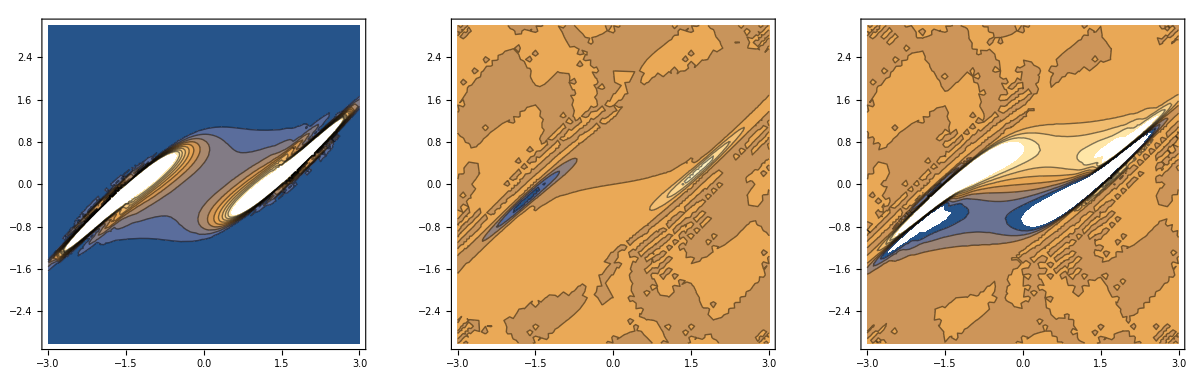

```mathematica
GraphicsRow[{ContourPlot[Abs[Evaluate[ϕ[[1]]]/Z],{x,-3,3},{y,-3,3},PlotRange->{0,0.2}],ContourPlot[Evaluate[ϕ[[2]]],{x,-3,3},{y,-3,3},PlotRange->All],ContourPlot[Evaluate[ϕ[[3]]],{x,-3,3},{y,-3,3},PlotRange->{-0.2,0.2}]}]
```

```mathematica
{λ,ϕ}=Module[{d=0.8^2/2,τ=2,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=Quiet[NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},3,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}}]]
];
```

```mathematica
Plot3D[Evaluate[ϕ[[2]]],{x,-3,3},{y,-3,3},PlotRange->All]
```

-Graphics3D-

The Backward Fokker-Planck operator is:
L^+=[sΦ(x)-x+(1-1/τ)y]∂_x  +D/τ(∂_x)^2  -y/τ∂_y  +D/τ(∂_y)^2 +2 D/τ∂_y ∂_x 
The eigenvalues must be the same:

```mathematica
{λ,ϕ}=Module[{d=0.8^2/2,τ=10,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=Quiet[NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},10,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}]]
];
Print["λ L: ",λ]
```

λ L: {-1.71845×10^-12,-0.100017,-0.124328,-0.200015,-0.300006,-0.399986,-0.500008,-0.471286-0.267126 ⅈ,-0.471286+0.267126 ⅈ,-0.599989}

```mathematica
{λt,ψ}=Module[{d=0.8^2/2,τ=10,s=1.5,λ,L=5,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]+(s*Tanh[x]-x +(1-1/τ)*y)*D[(u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]-y/τ*D[(u[x,y]), y] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},10,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}]]
];
Print["λ L^+: ",λt]
```

λ L^+: {-2.33021×10^-9,-0.1,-0.124353,-0.200001,-0.300015,-0.400111,-0.500584,-0.471343-0.267072 ⅈ,-0.471343+0.267072 ⅈ,-0.602409}

```mathematica
GraphicsRow[Table[ContourPlot[Evaluate[ϕ[[n]]],{x,-4,4},{y,-4,4},PlotRange->{-0.2,0.2}],{n,1,10}]]
```

-Graphics-

r,h domain with fictitious  diffusion

```mathematica
{λ,ϕ}=Module[{d=1^2/2,τ=1,s=1.5,L=6,ϵ=0.01},
ℒ=ϵ*D[D[u[r,h], r], r]-D[((Tanh[s*r +h]-r )*u[r,h]), r]+d/τ*D[D[u[r,h], h], h]+D[(h/τ*u[r,h]), h] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[r,h]==0,True]},u[r,h],{r,-3,3},{h,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}}]]
];
```

```mathematica
Print[λ]
```

{-7.30119×10^-14,-0.100001,-0.169907,-0.200003}

```mathematica
{λt,ψ}=Module[{d=1^2/2,τ=1,s=1.5,L=6,ϵ=0.01},
ℒ=ϵ*D[D[u[r,h], r], r]+(Tanh[s*r +h]-r )*D[(u[r,h]), r]+d/τ*D[D[u[r,h], h], h]-h/τ*D[(u[r,h]), h] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[r,h]==0,True]},u[r,h],{r,-3,3},{h,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.01}}}]]
];
Print[λt]
```

{-2.30715×10^-12,-0.199129,-0.864674,-1.00002}

```mathematica
Table[ContourPlot[Evaluate[ψ[[n]]],{r,-1.5,1.5},{h,-1.5,1.5}],{n,1,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Zϕ=NIntegrate[Evaluate[ϕ[[1]]],{r,-3,3},{h,-3,3}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
pp2=GraphicsColumn[{ ContourPlot[Evaluate[ϕ[[1]]]/Zϕ,{r,-1.5,1.5},{h,-1.8,1.8},PlotRange->All,ColorFunction->GrayLevel,PlotLegends->Automatic,Contours->8],ContourPlot[Evaluate[ϕ[[2]]],{r,-1.5,1.5},{h,-1.8,1.8},PlotRange->All,ColorFunction->GrayLevel,Contours->10,PlotLegends->Automatic],ContourPlot[Evaluate[ψ[[2]]],{r,-1.5,1.5},{h,-1.8,1.8},PlotRange->All,ColorFunction->GrayLevel,PlotLegends->Automatic]}]
```

-Graphics-

```mathematica
pp=GraphicsColumn[{ ContourPlot[Evaluate[ϕ[[1]]]/Zϕ,{r,-1.5,1.5},{h,-1.8,1.8},PlotRange->All,ColorFunction->GrayLevel,PlotLegends->Automatic],ContourPlot[Evaluate[ϕ[[2]]],{r,-1.5,1.5},{h,-1.8,1.8},PlotRange->All,ColorFunction->GrayLevel,Contours->10,PlotLegends->Automatic],ContourPlot[Evaluate[ψ[[2]]],{r,-1.5,1.5},{h,-1.8,1.8},PlotRange->All,ColorFunction->GrayLevel,PlotLegends->Automatic]}]
```

-Graphics-

```mathematica
GraphicsRow[{ContourPlot[Evaluate[ϕ[[2]]/(ϕ[[1]]*Zϕ)],{r,-1.2,1.2},{h,-1.4,1.4}],ContourPlot[Evaluate[ψ[[2]]/Zψ],{r,-1.2,1.2},{h,-1.4,1.4}]}]
```

-Graphics-

```mathematica
τs=10^Range[-0.5,1,0.2];
```

```mathematica
Σ=Table[Module[{τ=τs[[k]],σ=0.8,ϕ,ψ,λ,λt,Zϕ,Zψ},
{λ,ϕ}=Module[{d=σ^2/2,s=1.5,L=6,ϵ=0.01},
ℒ=ϵ*D[D[u[r,h], r], r]-D[((Tanh[s*r +h]-r )*u[r,h]), r]+d/τ*D[D[u[r,h], h], h]+D[(h/τ*u[r,h]), h] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[r,h]==0,True]},u[r,h],{r,-3,3},{h,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.01}}}]]
];
{λt,ψ}=Module[{d=σ^2/2,s=1.5,L=6,ϵ=0.01},
ℒ=ϵ*D[D[u[r,h], r], r]+(Tanh[s*r +h]-r )*D[(u[r,h]), r]+d/τ*D[D[u[r,h], h], h]-h/τ*D[(u[r,h]), h] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[r,h]==0,True]},u[r,h],{r,-3,3},{h,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.01}}}]]
];
Zϕ=Quiet[NIntegrate[Evaluate[ϕ[[2]]^2/ϕ[[1]]],{r,-1.2,1.2},{h,-1.4,1.4}]];
Zψ=Quiet[NIntegrate[Evaluate[ψ[[2]]*ϕ[[2]]],{r,-1.2,1.2},{h,-1.4,1.4}]];
Print["τ: ",τ,"  Δλ: ",Abs[λ[[2]]-λt[[2]]]];
Quiet[NIntegrate[Evaluate[(ϕ[[2]]^2/(Zϕ*ϕ[[1]])-ψ[[2]]/Zψ)^2],{r,-1.2,1.2},{h,-1.4,1.4}]]
],{k,1,Length[τs]}]
```

τ: 0.316228  Δλ: 5.13399×10^-8

τ: 0.501187  Δλ: 1.89689×10^-7

τ: 0.794328  Δλ: 2.24881×10^-7

τ: 1.25893  Δλ: 0.0000225039

τ: 1.99526  Δλ: 3.04644×10^-6

τ: 3.16228  Δλ: 4.68846×10^-8

τ: 5.01187  Δλ: 8.13534×10^-6

τ: 7.94328  Δλ: 0.0000173954

{2.60706,2.85734,3.45113,6.10025×10^7,4.56069×10^8,28.7479,219.316,1736.38}

```mathematica
Module[{τ=5,ϵ=0.1,σ=0.8,ϕ,ψ,λ,λt,Zϕ,Zψ,grid=0.01},
{λ,ϕ}=Module[{d=σ^2/2,s=1.5,L=6},
ℒ=ϵ*D[D[u[r,h], r], r]-D[((Tanh[s*r +h]-r )*u[r,h]), r]+d/τ*D[D[u[r,h], h], h]+D[(h/τ*u[r,h]), h] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[r,h]==0,True]},u[r,h],{r,-3,3},{h,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->grid}}}]]
];
{λt,ψ}=Module[{d=σ^2/2,s=1.5,L=6},
ℒ=ϵ*D[D[u[r,h], r], r]+(Tanh[s*r +h]-r )*D[(u[r,h]), r]+d/τ*D[D[u[r,h], h], h]-h/τ*D[(u[r,h]), h] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[r,h]==0,True]},u[r,h],{r,-3,3},{h,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->grid}}}]]
];
Zϕ=Quiet[NIntegrate[Evaluate[ϕ[[2]]^2/ϕ[[1]]],{r,-1.2,1.2},{h,-1.4,1.4}]];
Zψ=Quiet[NIntegrate[Evaluate[ψ[[2]]*ϕ[[2]]],{r,-1.2,1.2},{h,-1.4,1.4}]];
Print["τ: ",τ,"  Δλ: ",Abs[λ[[2]]-λt[[2]]]];
Print["D: ",σ^2/(2*τ),"  ϵ: ",ϵ];
GraphicsRow[{ContourPlot[Evaluate[ϕ[[1]]],{r,-1.2,1.2},{h,-1.4,1.4}],ContourPlot[Evaluate[ϕ[[2]]/(ϕ[[1]]*Zϕ)],{r,-1.2,1.2},{h,-1.4,1.4}],ContourPlot[Evaluate[ψ[[2]]/Zψ],{r,-1.2,1.2},{h,-1.4,1.4}]}]
]
```

τ: 5  Δλ: 2.74013×10^-8

D: 0.064  ϵ: 0.1

-Graphics-

Dominant eigenvalue:

```mathematica
τs=10^Range[-1,2,0.1];
```

σ=1

```mathematica
σt=1.0;
```

```mathematica
λs1=Parallelize[Table[Module[{d=σt^2/2,τ=τs[[k]],s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=Quiet[NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}]];
λ
],{k,1,Length[τs]}]];
```

```mathematica
λm1=Module[{d=σt^2/2,τ=1-0.01,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
];
λp1=Module[{d=σt^2/2,τ=1+0.01,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
];
```

```mathematica
dλ1dτ=(λp[[2]]-λm[[2]])/(2*0.01)
```

-0.0414226

```mathematica
λ11=Module[{d=σt^2/2,τ=1,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
][[2]]
```

-0.192745

```mathematica
fλ1[τ_]:=Max[{ λ11+dλ1dτ*(1-1/τ),-1/τ}]
```

```mathematica
Show[{LogLinearPlot[fλ1[τ],{τ,0.1,100},PlotRange->{-0.4,-0.01}],ListLogLinearPlot[Transpose[{τs,λs1[[All,1]]}],PlotRange->{-0.4,-0.01}],ListLogLinearPlot[Transpose[{τs,λs1[[All,2]]}],PlotRange->{-0.4,-0.01}]}]
```

-Graphics-

σ=0.8

```mathematica
σt=0.8;
```

```mathematica
λs8=Parallelize[Table[Module[{d=σt^2/2,τ=τs[[k]],s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=Quiet[NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}]];
λ
],{k,1,Length[τs]}]];
```

```mathematica
λm8=Module[{d=σt^2/2,τ=1-0.01,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
];
λp8=Module[{d=σt^2/2,τ=1+0.01,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
];
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[<1337973>, {86021, 86021}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
dλ8dτ=(λp8[[2]]-λm8[[2]])/(2*0.01)
```

-0.0433589

```mathematica
λ18=Module[{d=σt^2/2,τ=1,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
][[2]]
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[<1337973>, {86021, 86021}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

-0.132988

```mathematica
fλ18[τ_]:=Max[{ λ18+dλ8dτ*(1-1/τ),-1/τ}]
```

```mathematica
Show[{LogLinearPlot[fλ18[τ],{τ,0.1,100},PlotRange->{-0.4,-0.01}],ListLogLinearPlot[Transpose[{τs,λs8[[All,1]]}],PlotRange->{-0.4,-0.01}],ListLogLinearPlot[Transpose[{τs,λs8[[All,2]]}],PlotRange->{-0.4,-0.01}]}]
```

-Graphics-

σ=0.6

```mathematica
σt=0.6;
```

```mathematica
λs6=Parallelize[Table[Module[{d=σt^2/2,τ=τs[[k]],s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=Quiet[NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}]];
λ
],{k,1,Length[τs]}]];
```

```mathematica
λm6=Module[{d=σt^2/2,τ=1-0.01,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
];
λp6=Module[{d=σt^2/2,τ=1+0.01,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
];
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[<1337973>, {86021, 86021}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
dλ6dτ=(λp6[[2]]-λm6[[2]])/(2*0.01)
```

-0.0414226

```mathematica
λ16=Module[{d=σt^2/2,τ=1,s=1.5,λ,L=6,ϕ},
ℒ=d/τ*D[D[u[x,y], x], x]-D[((s*Tanh[x]-x +(1-1/τ)*y)*u[x,y]), x]+2*d/τ*D[D[u[x,y], y], x]+d/τ*D[D[u[x,y], y], y]+D[(y/τ*u[x,y]), y] ;
{λ,ϕ}=NDEigensystem[{ℒ,DirichletCondition[u[x,y]==0,True]},u[x,y],{x,-L,L},{y,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.005}}}];
λ
][[2]]
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[<1337973>, {86021, 86021}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

-0.0713584

```mathematica
fλ6[τ_]:=Max[{ λ16+dλ6dτ*(1-1/τ),-1/τ}]
```

```mathematica
Show[{LogLinearPlot[fλ6[τ],{τ,0.1,100},PlotRange->{-0.4,-0.01}],ListLogLinearPlot[Transpose[{τs,λs6[[All,1]]}],PlotRange->{-0.4,-0.01}],ListLogLinearPlot[Transpose[{τs,λs6[[All,2]]}],PlotRange->{-0.4,-0.01}]}]
```

-Graphics-

```mathematica
τs2=10^Range[-1,2,0.01];
SetDirectory[NotebookDirectory[]];
Export["DataSetDominantEignvalues.h5",{"Tau"->τs,"Tau2"->τs2,"g6"->Table[fλ6[τs2[[n]]],{n,1,Length[τs2]}],"g8"->Table[fλ18[τs2[[n]]],{n,1,Length[τs2]}],"g1"->Table[fλ1[τs2[[n]]],{n,1,Length[τs2]}],"l1"-> Re[λs1],"l6"-> Re[λs6],"l8"-> Re[λs8]}]
```

DataSetDominantEignvalues.h5

Linear Response:

m_σ=∫rϕ_0(r,h)drdh

```mathematica
τs= 10.^Range[Log10[3],1,0.05]
m0=Parallelize[Table[Module[{ϕ,λ,τ=τs[[k]],σ=0.5,Z},
{λ,ϕ}=Module[{d=σ^2/2,s=1.5,L=6,ϵ=0.005},
ℒ=ϵ*D[D[u[r,h], r], r]-D[((Tanh[s*r +h]-r )*u[r,h]), r]+d/τ*D[D[u[r,h], h], h]+D[(h/τ*u[r,h]), h] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[r,h]==0,True]},u[r,h],{r,-3,3},{h,-L,L},2,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.01}}}]]
];
Z=Quiet[NIntegrate[Evaluate[ϕ[[1]]],{r,-2.9,2.9},{h,-5.9,5.9}]];

Quiet[NIntegrate[r*Evaluate[ϕ[[1]]],{r,-2.9,2.9},{h,-5.9,5.9}]]/Z
],{k,1,Length[τs]}]];
```

```mathematica
ListLogLogPlot[Transpose[{τs,Abs[m0]}],PlotRange->All]
```

-Graphics-

u_n=∫rϕ_n(r,h)drdh
c_n0=-∫ψ_n(r,h)∂_σ ϕ_0(r,h)drdh=σ/λ_n<ψ_n|(∂_h)^2 ϕ_0>

```mathematica
τs= 10.^Range[Log10[3],1,0.05];
τs= Range[3,10,0.2];
r=Parallelize[Table[Module[{ϕ,ψ,λ,λt,Indϕ,Indψ,τ=τs[[k]],σ=1,Z,u,c,grid=0.01,L=6.5,ϵ=0.01},
{λ,ϕ}=Module[{d=σ^2/2,s=1.5},
ℒ=ϵ*D[D[u[r,h], r], r]-D[((Tanh[s*r +h]-r )*u[r,h]), r]+d/τ*D[D[u[r,h], h], h]+D[(h/τ*u[r,h]), h] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[r,h]==0,True]},u[r,h],{r,-3.5,3.5},{h,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->grid}}}]]
];
{λt,ψ}=Module[{d=σ^2/2,s=1.5},
ℒ=ϵ*D[D[u[r,h], r], r]+(Tanh[s*r +h]-r )*D[(u[r,h]), r]+d/τ*D[D[u[r,h], h], h]-h/τ*D[(u[r,h]), h] ;
Quiet[NDEigensystem[{ℒ,DirichletCondition[u[r,h]==0,True]},u[r,h],{r,-3.5,3.5},{h,-L,L},4,Method->{"Eigensystem"->{"Method"->"Direct"},"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->grid}}}]]
];
Indϕ=If[Abs[λ[[1]]]>0.001,1,2];
Indψ=If[Abs[λt[[1]]]>0.001,1,2];
Z=Quiet[NIntegrate[Evaluate[ϕ[[Indϕ]]*ψ[[Indψ]]],{r,-3.4,3.4},{h,-L+0.1, L-0.1}]];
u=Quiet[NIntegrate[r*Evaluate[ϕ[[Indϕ]]],{r,-3.4,3.4},{h,-5.9,5.9}]]/Z;
c=Quiet[σ*NIntegrate[Evaluate[ψ[[Indψ]]]*Evaluate[D[D[ϕ[[1]], h], h]],{r,-3.4,3.4},{h,-5.9,5.9}]/(λ[[Indϕ]]*Z*τ)];
{λ[[Indϕ]],u*c}

],{k,1,Length[τs]}]];
```

```mathematica
GraphicsRow[{ListLogLinearPlot[Transpose[{τs,r[[All,1]]}]],ListLogLinearPlot[Transpose[{τs,r[[All,2]]}]]}]
```

-Graphics-

```mathematica
ω=0.01*2*π;
χ=Table[(r[[n,2]]ⅈ*ω)/(r[[n,1]]-ⅈ*ω),{n,1,Length[τs]}];
ListPlot[Transpose[{τs,Abs[χ]}],Joined->True,PlotRange->{{3,9},{0,15}}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{τs,r[[All,1]]}],Joined->True,PlotRange->{{3,9},{-0.25,-0.05}}]
```

-Graphics-